```mathematica
ds=ResourceData["Epidemic Data for Novel Coronavirus 2019-nCoV from Wuhan, China"]
```

Dataset[<>]

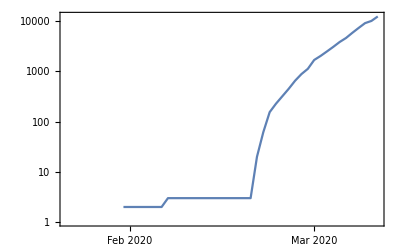

```mathematica
DateListLogPlot[ds[2, "ConfirmedCases"]]
```

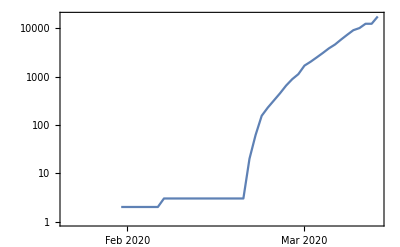

```mathematica
DateListLogPlot[ds[2, "ConfirmedCases"]]
```

```mathematica
ds[All, "Country"]
```

Dataset[<>]

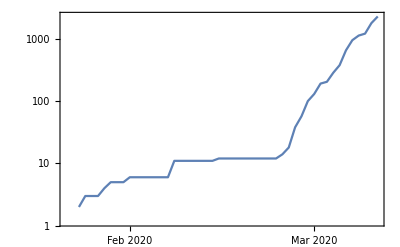

```mathematica
DateListLogPlot[ds[5, "ConfirmedCases"]]
```

```mathematica
Keys@ds
```

Dataset[<>]

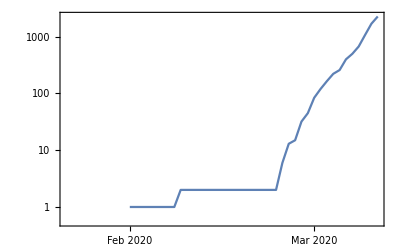

```mathematica
DateListLogPlot[ds[6, "ConfirmedCases"]]
```

```mathematica
dataset=Dataset[{<|"a"->1,"b"->"x","c"->{1}|>,<|"a"->2,"b"->"y","c"->{2,3}|>,<|"a"->3,"b"->"z","c"->{3}|>,<|"a"->4,"b"->"x","c"->{4,5}|>,<|"a"->5,"b"->"y","c"->{5,6,7}|>,<|"a"->6,"b"->"z","c"->{}|>}]
```

Dataset[<>]

```mathematica
dataset[GroupBy["a"]]
```

Dataset[<>]

```mathematica
dsGrouped=ds[GroupBy["Country"]];
```

```mathematica
Keys@dsGrouped
```

Dataset[<>]

```mathematica
outsideChinaDs=Rest[dsGrouped];
```

```mathematica
outsideChinaDs[Total, "ConfirmedCases"]
```

Failure[…]

```mathematica
dsChina=dsGrouped[1];
```

DateListLogPlot::ldata: … is not a valid dataset or list of datasets.

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

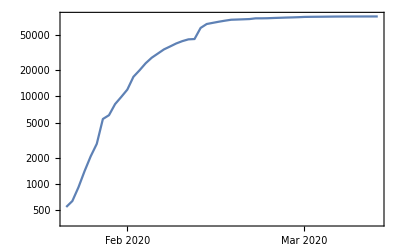
Show[-Graphics-,DateListLogPlot[Failure[…]]]

```mathematica
Show[DateListLogPlot[dsChina[Total, "ConfirmedCases"]],DateListLogPlot[outsideChinaDs[Total, "ConfirmedCases"]]]
```

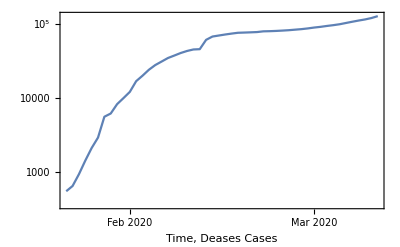

```mathematica
DateListLogPlot[ds[Total, "ConfirmedCases"], AxesLabel->{"Time, Deases Cases"}]
```

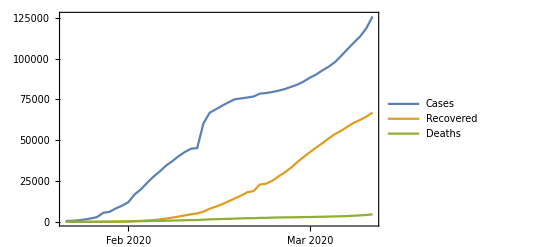

```mathematica
DateListPlot[{ds[Total, "ConfirmedCases"],ds[Total, "RecoveredCases"],ds[Total, "Deaths"]}, PlotLegends->{"Cases","Recovered", "Deaths"}]
```

### Useful link: https://blog.wolfram.com/2014/11/04/modeling-a-pandemic-like-ebola-with-the-wolfram-language/

```mathematica
ds[Select[#Country≠"China"&]]
```

Dataset[<>]

```mathematica
Plot
```

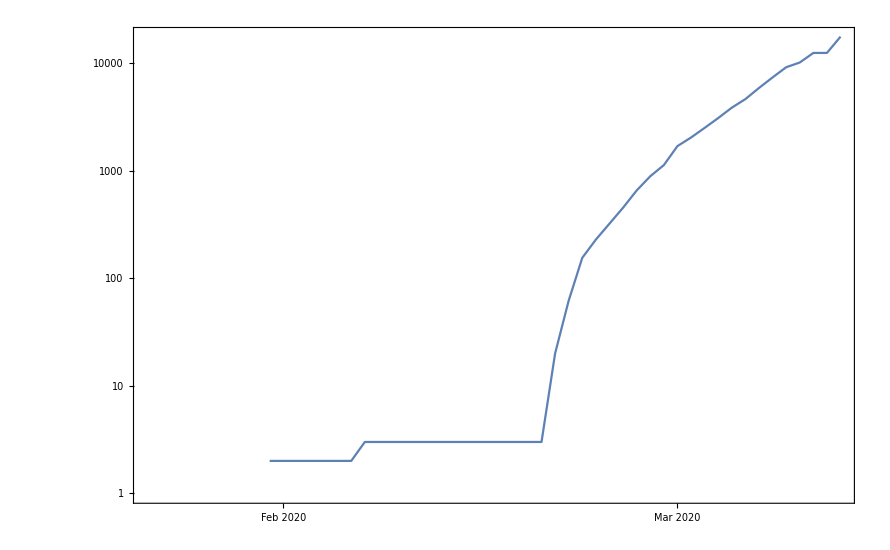

```mathematica
DateListLogPlot[ds[2,"ConfirmedCases"],DateTicksFormat->"Day"]
```